{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

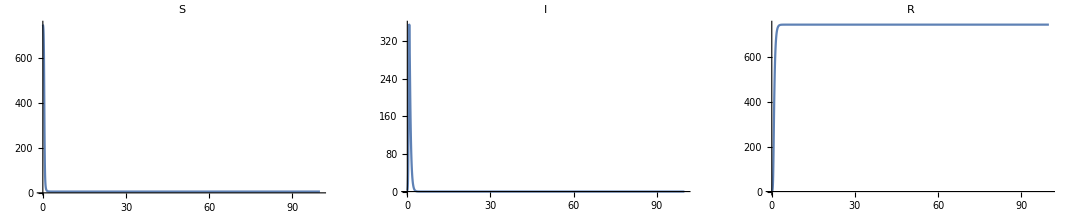

```mathematica
r=0.0178;
a=2.73;
Clear[S,Inf,R];
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==750,Inf[0]==2,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All,PlotLabel-> "S"],Plot[Inf[t],{t,0,100},PlotRange->All,PlotLabel-> "I"],Plot[R[t],{t,0,100},PlotRange->All,PlotLabel-> "R"]}]
```

2

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

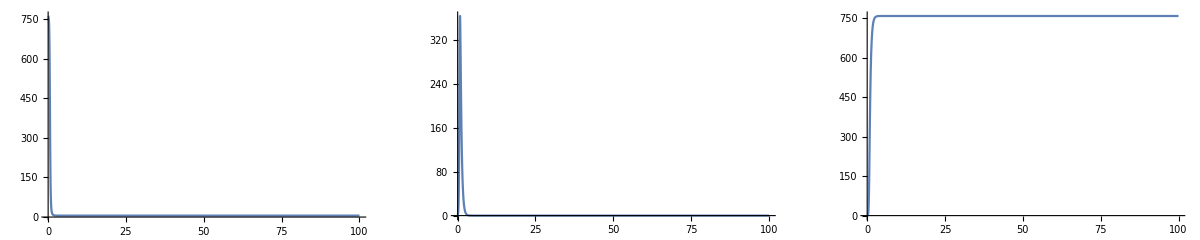

```mathematica
Clear[S,Inf,R];
r=0.0178;
a=2.73;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==762,Inf[0]==1,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

3

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

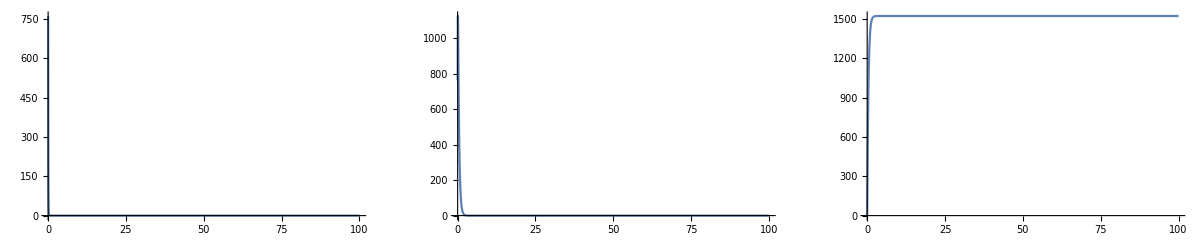

```mathematica
Clear[S,Inf,R];
r=0.0178;
a=2.73;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==762,Inf[0]==762,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

4

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

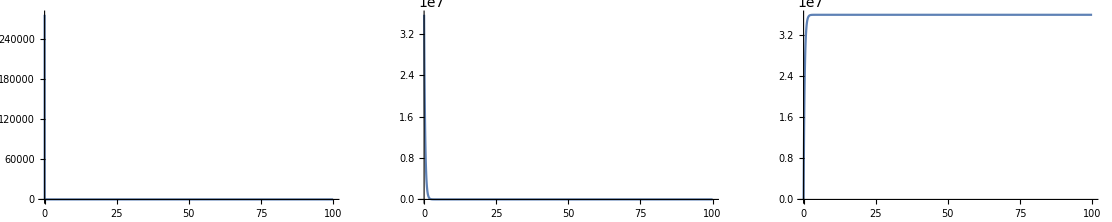

```mathematica
Clear[S,Inf,R];
r=0.0178;
a=2.73;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==1000000,Inf[0]==35000000,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

5

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

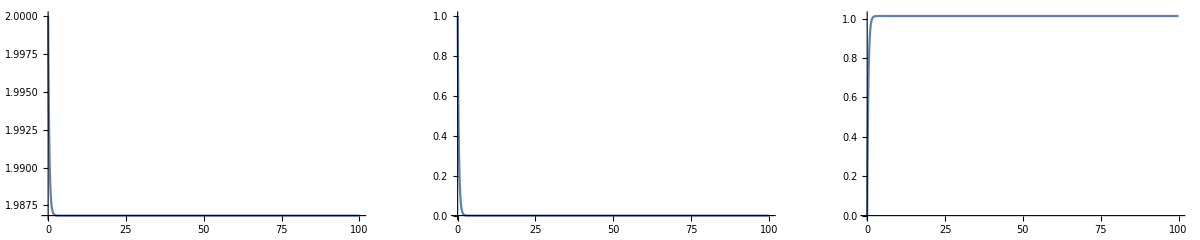

```mathematica
Clear[S,Inf,R];
r=0.0178;
a=2.73;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==2,Inf[0]==1,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

6

{S→InterpolatingFunction[{{0., 1.}}, <>],Inf→InterpolatingFunction[{{0., 1.}}, <>],R→InterpolatingFunction[{{0., 1.}}, <>]}

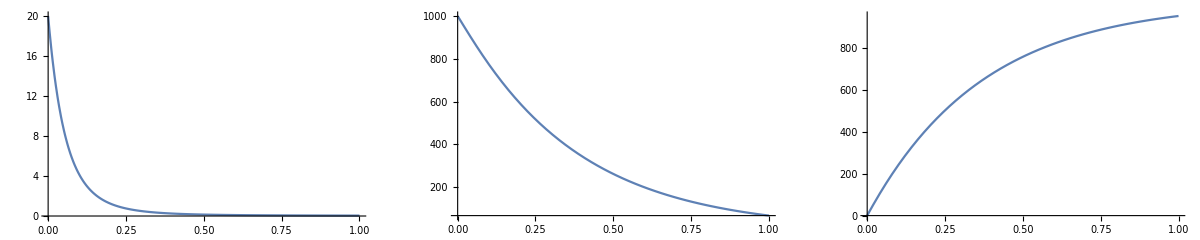

```mathematica
Clear[S,Inf,R];
r=0.0178;
a=2.73;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==20,Inf[0]==1000,R[0]==0},{S,Inf,R},{t,0,1}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,1},PlotRange->All],Plot[Inf[t],{t,0,1},PlotRange->All],Plot[R[t],{t,0,1},PlotRange->All]}]
```

7

{S→InterpolatingFunction[{{0., 1.}}, <>],Inf→InterpolatingFunction[{{0., 1.}}, <>],R→InterpolatingFunction[{{0., 1.}}, <>]}

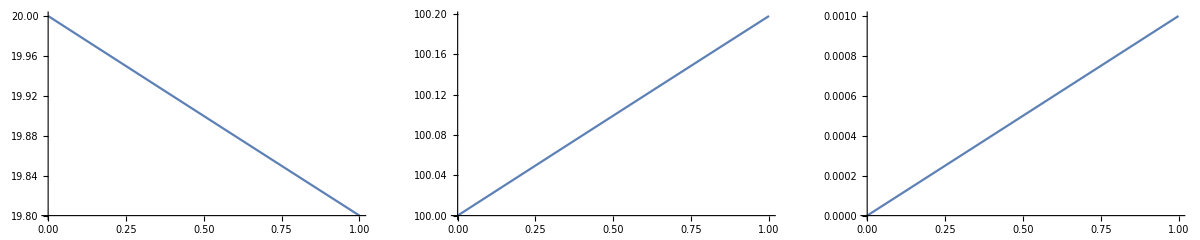

```mathematica
Clear[S,Inf,R];
r=0.0001;
a=0.00001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==20,Inf[0]==100,R[0]==0},{S,Inf,R},{t,0,1}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,1},PlotRange->All],Plot[Inf[t],{t,0,1},PlotRange->All],Plot[R[t],{t,0,1},PlotRange->All]}]
```

8

{S→InterpolatingFunction[{{0., 1000.}}, <>],Inf→InterpolatingFunction[{{0., 1000.}}, <>],R→InterpolatingFunction[{{0., 1000.}}, <>]}

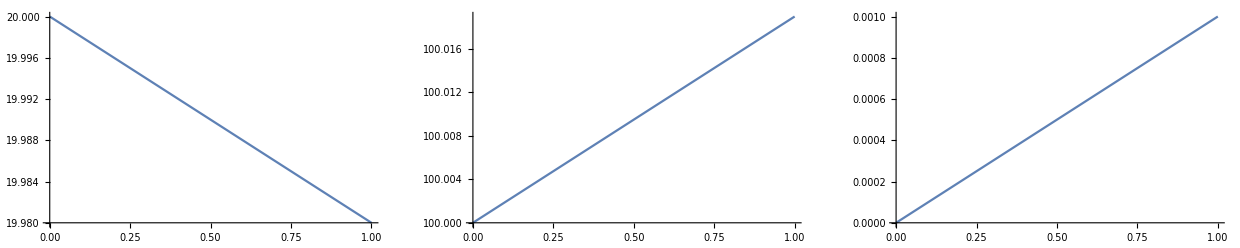

```mathematica
Clear[S,Inf,R];
r=0.00001;
a=0.00001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==20,Inf[0]==100,R[0]==0},{S,Inf,R},{t,0,1000}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,1},PlotRange->All],Plot[Inf[t],{t,0,1},PlotRange->All],Plot[R[t],{t,0,1},PlotRange->All]}]
```

9

{S→InterpolatingFunction[{{0., 10.}}, <>],Inf→InterpolatingFunction[{{0., 10.}}, <>],R→InterpolatingFunction[{{0., 10.}}, <>]}

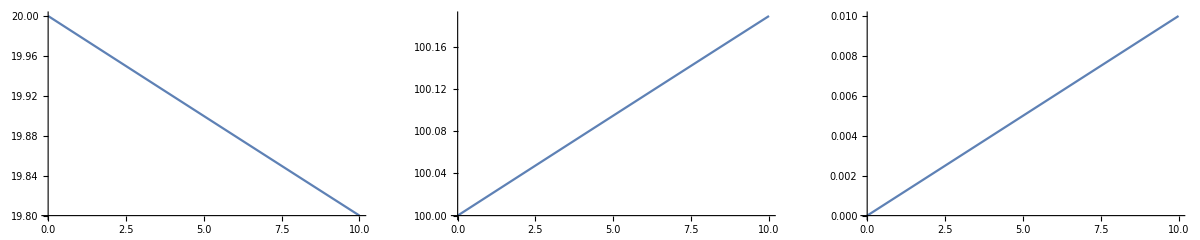

```mathematica
Clear[S,Inf,R];
r=0.00001;
a=0.00001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==20,Inf[0]==100,R[0]==0},{S,Inf,R},{t,0,10}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,10},PlotRange->All],Plot[Inf[t],{t,0,10},PlotRange->All],Plot[R[t],{t,0,10},PlotRange->All]}]
```

10

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

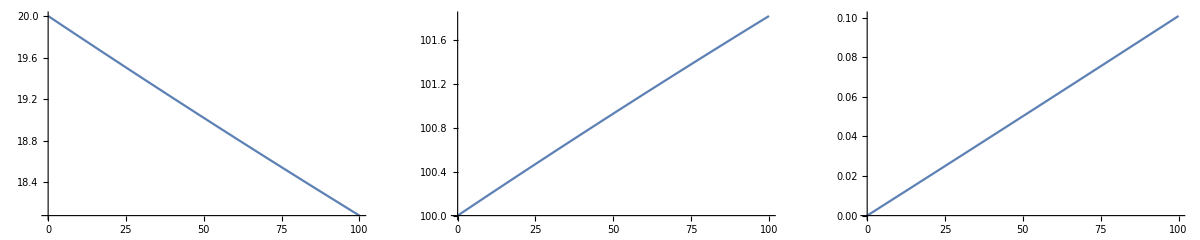

```mathematica
Clear[S,Inf,R];
r=0.00001;
a=0.00001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==20,Inf[0]==100,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

11

{S→InterpolatingFunction[{{0., 10.}}, <>],Inf→InterpolatingFunction[{{0., 10.}}, <>],R→InterpolatingFunction[{{0., 10.}}, <>]}

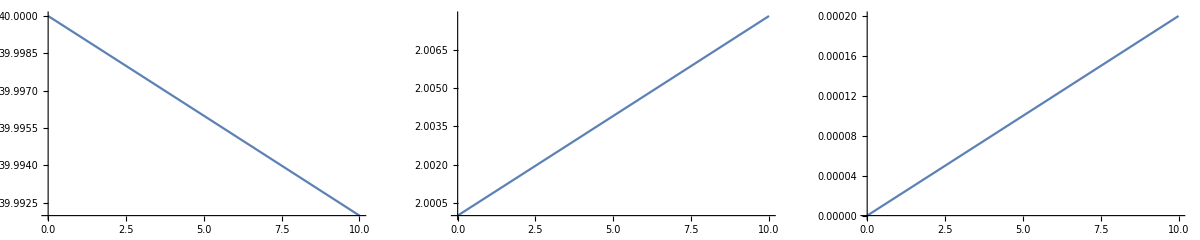

```mathematica
Clear[S,Inf,R];
r=0.00001;
a=0.00001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==40,Inf[0]==2,R[0]==0},{S,Inf,R},{t,0,10}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,10},PlotRange->All],Plot[Inf[t],{t,0,10},PlotRange->All],Plot[R[t],{t,0,10},PlotRange->All]}]
```

12

```mathematica
Clear[S,Inf,R];
r=0.00001;
a=0.00001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==40,Inf[0]==2,R[0]==0},{S,Inf,R},{t,0,10}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,10},PlotRange->All],Plot[Inf[t],{t,0,10},PlotRange->All],Plot[R[t],{t,0,10},PlotRange->All]}]
```

{S→InterpolatingFunction[{{0., 10.}}, <>],Inf→InterpolatingFunction[{{0., 10.}}, <>],R→InterpolatingFunction[{{0., 10.}}, <>]}

-Graphics-

13

{S→InterpolatingFunction[{{0., 1000.}}, <>],Inf→InterpolatingFunction[{{0., 1000.}}, <>],R→InterpolatingFunction[{{0., 1000.}}, <>]}

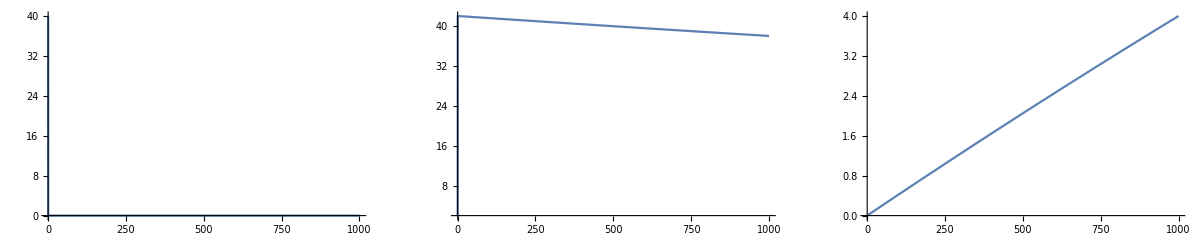

```mathematica
Clear[S,Inf,R];
r=3.78;
a=0.0001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==40,Inf[0]==2,R[0]==0},{S,Inf,R},{t,0,1000}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,1000},PlotRange->All],Plot[Inf[t],{t,0,1000},PlotRange->All],Plot[R[t],{t,0,1000},PlotRange->All]}]
```

14

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

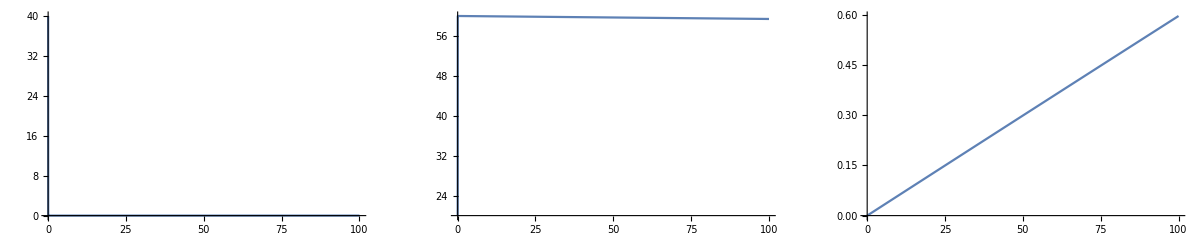

```mathematica
Clear[S,Inf,R];
r=3.78;
a=0.0001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==40,Inf[0]==20,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

15

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

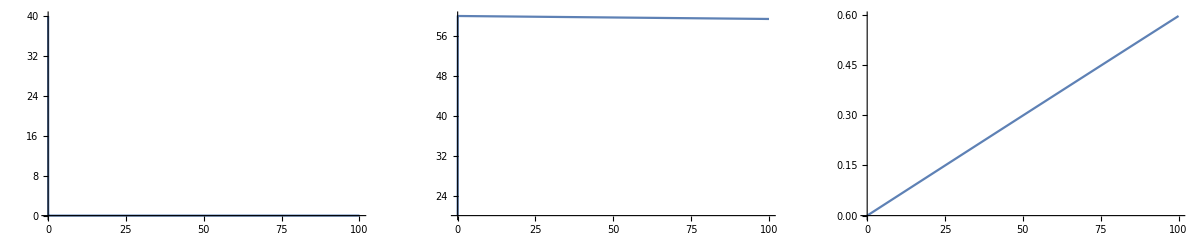

```mathematica
Clear[S,Inf,R];
r=5.00;
a=0.0001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==40,Inf[0]==20,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

16

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

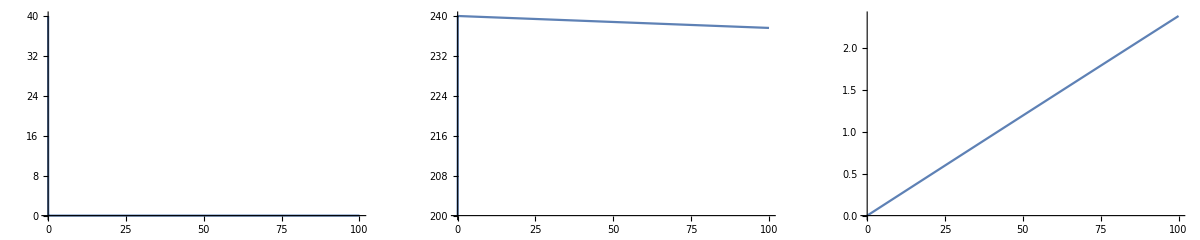

```mathematica
Clear[S,Inf,R];
r=5.00;
a=0.0001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==40,Inf[0]==200,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

17

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

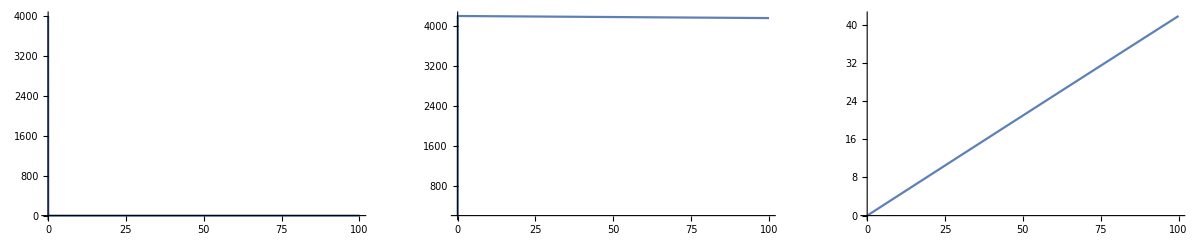

```mathematica
Clear[S,Inf,R];
r=5.00;
a=0.0001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==4000,Inf[0]==200,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

18

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

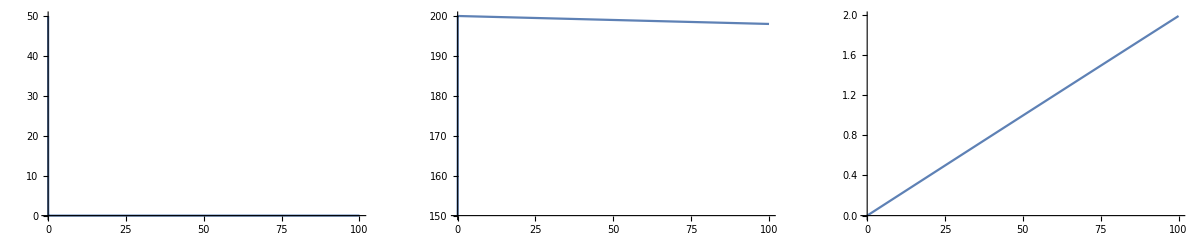

```mathematica
Clear[S,Inf,R];
r=5.00;
a=0.0001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==50,Inf[0]==150,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

19

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

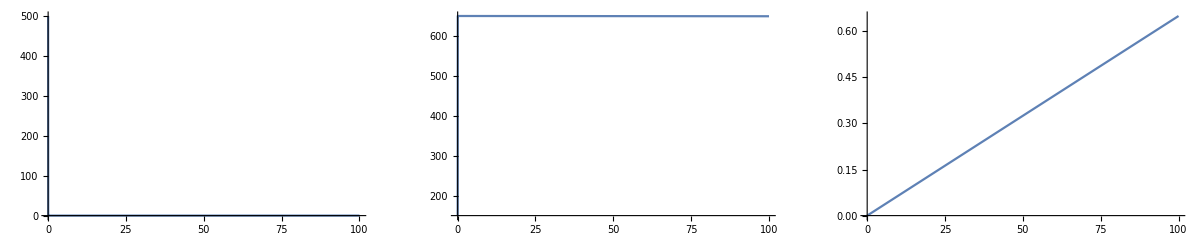

```mathematica
Clear[S,Inf,R];
r=5.00;
a=0.00001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==500,Inf[0]==150,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

20

{S→InterpolatingFunction[{{0., 100000.}}, <>],Inf→InterpolatingFunction[{{0., 100000.}}, <>],R→InterpolatingFunction[{{0., 100000.}}, <>]}

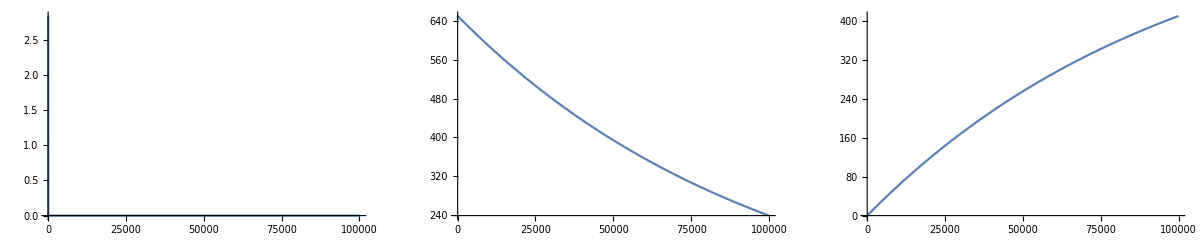

```mathematica
Clear[S,Inf,R];
r=5.00;
a=0.00001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==500,Inf[0]==150,R[0]==0},{S,Inf,R},{t,0,100000}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100000},PlotRange->All],Plot[Inf[t],{t,0,100000},PlotRange->All],Plot[R[t],{t,0,100000},PlotRange->All]}]
```

21

{S→InterpolatingFunction[{{0., 100000.}}, <>],Inf→InterpolatingFunction[{{0., 100000.}}, <>],R→InterpolatingFunction[{{0., 100000.}}, <>]}

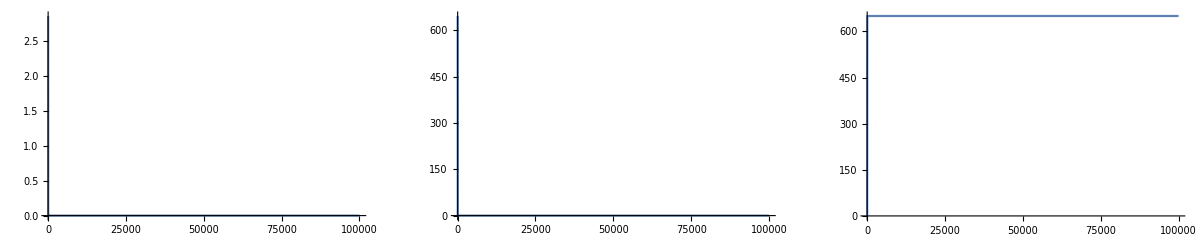

```mathematica
Clear[S,Inf,R];
r=5.00;
a=1.00;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==500,Inf[0]==150,R[0]==0},{S,Inf,R},{t,0,100000}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100000},PlotRange->All],Plot[Inf[t],{t,0,100000},PlotRange->All],Plot[R[t],{t,0,100000},PlotRange->All]}]
```

22

{S→InterpolatingFunction[{{0., 1000.}}, <>],Inf→InterpolatingFunction[{{0., 1000.}}, <>],R→InterpolatingFunction[{{0., 1000.}}, <>]}

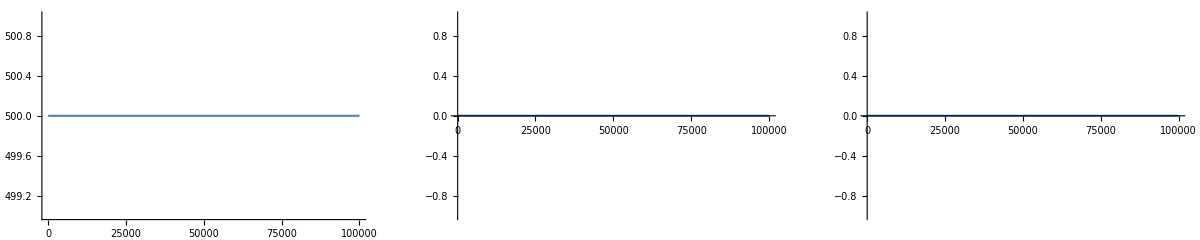

```mathematica
Clear[S,Inf,R];
r=5.00;
a=1.00;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==500,Inf[0]==0,R[0]==0},{S,Inf,R},{t,0,1000}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100000},PlotRange->All],Plot[Inf[t],{t,0,100000},PlotRange->All],Plot[R[t],{t,0,100000},PlotRange->All]}]
```

23

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

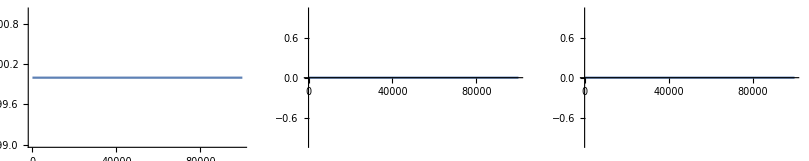

```mathematica
Clear[S,Inf,R];
r=5.00;
a=0.00001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==500,Inf[0]==0,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100000},PlotRange->All],Plot[Inf[t],{t,0,100000},PlotRange->All],Plot[R[t],{t,0,100000},PlotRange->All]}]
```

24

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

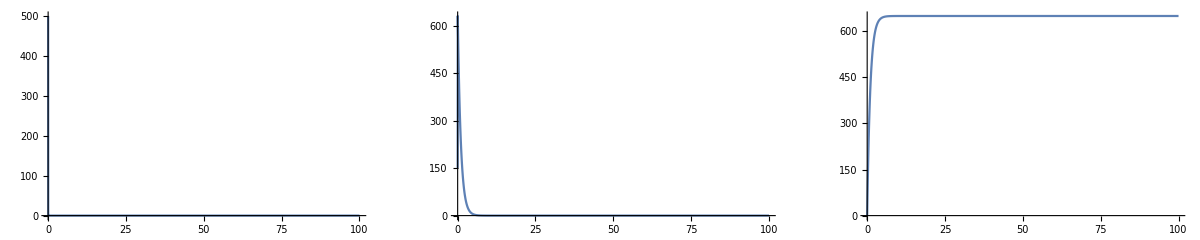

```mathematica
Clear[S,Inf,R];
r=5.00;
a=1.00;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==500,Inf[0]==150,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

25

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

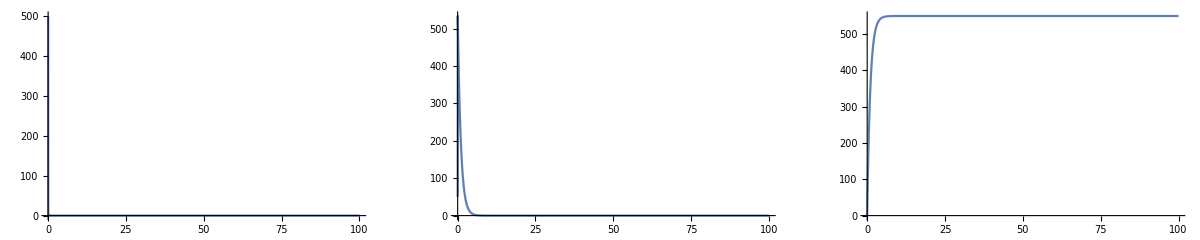

```mathematica
Clear[S,Inf,R];
r=5.00;
a=1.00;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==500,Inf[0]==50,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

26

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

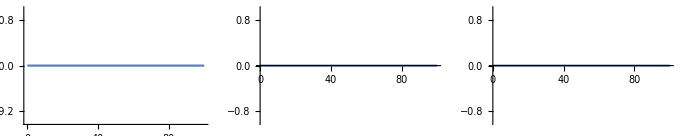

```mathematica
Clear[S,Inf,R];
r=5.00;
a=1.00;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==500,Inf[0]==0,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

27

```mathematica
Clear[S,Inf,R];
r=5.00;
a=1.00;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==500,Inf[0]==50,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

-Graphics-

28

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

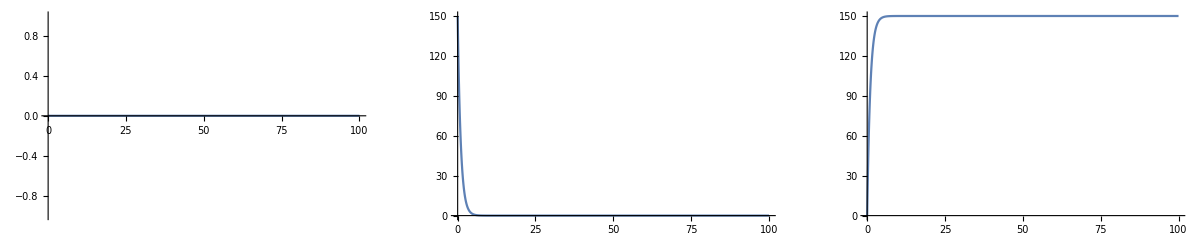

```mathematica
Clear[S,Inf,R];
r=5.00;
a=1.00;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==0,Inf[0]==150,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```

29

{S→InterpolatingFunction[{{0., 100.}}, <>],Inf→InterpolatingFunction[{{0., 100.}}, <>],R→InterpolatingFunction[{{0., 100.}}, <>]}

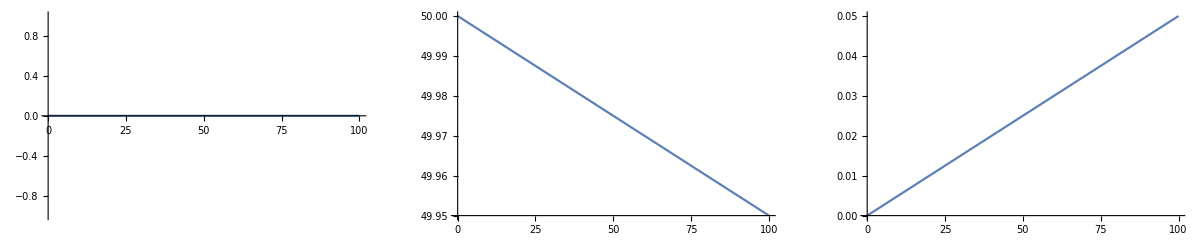

```mathematica
Clear[S,Inf,R];
r=5.00;
a=0.00001;
result=NDSolve[{S'[t]==-r S[t] Inf[t],Inf'[t]==r S[t] Inf[t]-a Inf[t], R'[t]==a Inf[t],S[0]==0,Inf[0]==50,R[0]==0},{S,Inf,R},{t,0,100}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,100},PlotRange->All],Plot[Inf[t],{t,0,100},PlotRange->All],Plot[R[t],{t,0,100},PlotRange->All]}]
```